### Slow-roll

```mathematica
p1=Plot[(h^2-v^2)^2/(1+10*h^2)^2,{h,0, 5}]
```

-Graphics-

```mathematica
U[h_,v_]:=λ/4((h^2-v^2)/(1+(ξ*h^2)/Subscript[M, p]^2))^2
D[U[h,v],h]


Solve[D[U[h, v],h] ==0,v]
```

(h (h^2-v^2) λ)/((1+(h^2 ξ)/M_p^2)^2)-(h (h^2-v^2)^2 λ ξ)/((1+(h^2 ξ)/M_p^2)^3 M_p^2)

{{v→-h},{v→h},{v→-(ⅈ M_p)/(√ξ)},{v→(ⅈ M_p)/(√ξ)}}

```mathematica
D[U[h,v],h]/.{v->-(ⅈ Subscript[M, p])/(√ξ)}//Simplify
```

0

```mathematica
s=NDSolve[{X'[y]==Sqrt[(1+(1+6*100)y^2)/(1+y^2)^2],X[0]==0},X,{y,0,100}]
```

{{X→InterpolatingFunction[…]}}

```mathematica
x1=Plot[Evaluate[X[y]/.s],{y,0,100},PlotRange->All];
```

```mathematica
x2=Plot[Sqrt[600]Log[x],{x,1,100},PlotStyle->Red];
```

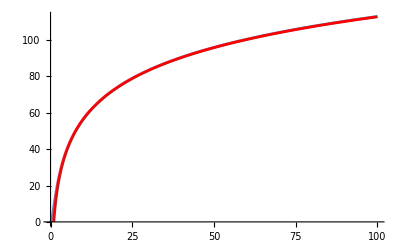

```mathematica
Show[x1,x2]
```

### Exploración del régimen Slow-Roll y Ultra Slow-Roll

```mathematica
s=NDSolve[{y''[t]+3*((1/2)*(1+Exp[-2*y[t]])^(-2)+(y'[t])^2)^(1/2)*y'[t]+(1+Exp[-2*y[t]])^(-3)*Exp[-2*y[t]]==0,y'[0]==5,y[0]==1},y,{t,0,250}]
```

{{y→InterpolatingFunction[…]}}

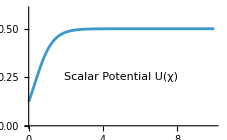

```mathematica
Plot[(1/2)*(1+Exp[-2*x])^(-2),{x,0,10},PlotRange->{{0,10},{0,0.6}},Epilog->{Inset["Scalar Potential U(χ)",{5,0.25}]}]
```

Then, for field values around y = 3 and up, the field potential is clearly flat.

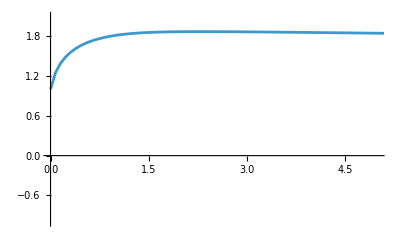

```mathematica
s1=Plot[Evaluate[y[t]/.s],{t,0,250},PlotRange->{{0,5},{-1,2.1}}](* Evolucion del campo χ *)
```

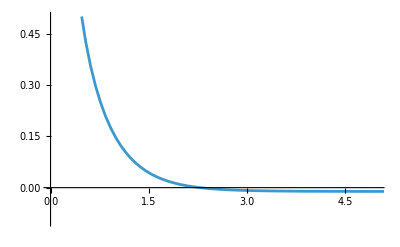

```mathematica
s2=Plot[Evaluate[y'[t]/.s],{t,0,250},PlotRange->{{0,5},{-0.1,0.5}}](* Evolucion de dχ/dt *)
```

```mathematica
s3=Plot[Evaluate[y''[t]/.s],{t,0,100},PlotRange->All] ;(* Evolucion de d^2 χ/dt^2  *)
```

Termino de fricción (rojo) versus termino de aceleración (azul).

```mathematica
e1=Plot[Evaluate[Abs[3*Sqrt[((1/2)*(1+Exp[-2*y[t]])^(-2)+(y'[t])^2)]*y'[t]]]/.s,{t,0,5},PlotRange->{{0,5},{-0.05,0.2}},PlotStyle->Red];
e2=Plot[Evaluate[Abs[y''[t]]/.s],{t,0,5},PlotRange->All];
e3=Plot[Evaluate[Abs[(1+Exp[-2*y[t]])^(-3)*Exp[-2*y[t]]]/.s,{t,0,5},PlotRange->{{0,5},{-0.05,0.2}},PlotStyle->Green]];
```

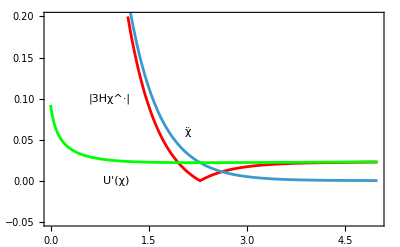

```mathematica
Show[e1,e2,e3,Frame->True,Axes->None,FrameLabel->{"t√(λ/6)M_p/ξ"},Epilog->{Inset["|3Hχ^·|",{0.9,0.1}],Inset["χ̈",{2.1,0.06}],Inset["U'(χ)",{1,0}]}]
```

```mathematica
Export["sol.png",%]
```

sol.png

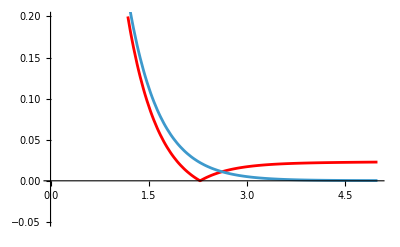

```mathematica
Show[e1,e2]
```

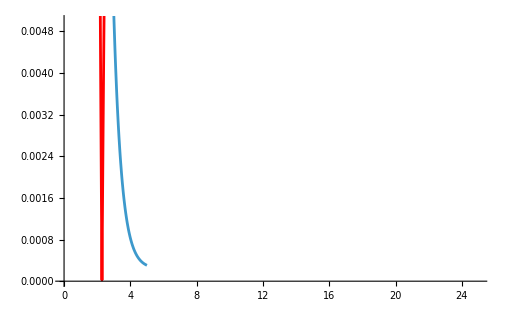

```mathematica
Show[e1,e2,PlotRange->{{0,25},{0,0.005}}]
```

```mathematica
Export["SR1.jpg",%]
```

SR1.jpg

Comparación de termino cinético 0.5*(dχ/dt)^2 (en verde)  versus   U(χ) en azul.

```mathematica
f1=Plot[Evaluate[Abs[0.5*(y'[t])^2]/.s],{t,0,5},PlotRange->All,PlotStyle->Green];
f2=Plot[Evaluate[Abs[0.25*(1+Exp[-2*y[t]/√6])^(-2)]/.s],{t,0,5},PlotRange->All];
```

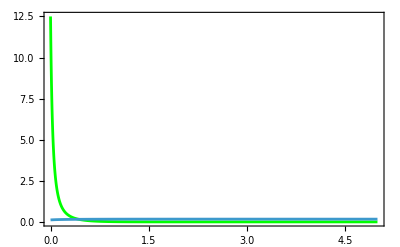

```mathematica
Show[f1,f2,Frame->True,FrameLabel->{"t√λM/ξ"},Epilog->{Inset["1/2(χ^·)^2",{150,0.03}],Inset["U(χ)",{100,0.20}]}]
```

```mathematica
Export["SR2.jpg",%]
```

SR2.jpg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["SR2.jpg"]]]
```

Número de e-foldings

```mathematica
NIntegrate[1/(√12)*√((1+Exp[-2*y[t]/√6])^(-2)+2*(y'[t])^2)/.s,{t,0,260}] (* Calculo exacto *)
```

{392.41}

```mathematica
Evaluate[3/4*(Exp[2*5.49/√6]-1)]/.s
```

{65.596}

```mathematica
N[√6 Log[9.4]]
```

5.4886

```mathematica
yt=5.4886;
```

```mathematica
Solve[ytp==-((1+Exp[-2*yt/√6])^(-3)*Exp[-2*yt/√6]/√6)/(√(3/4)*((1+Exp[-2*yt/√6])^(-2)+2*(ytp)^2))]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ytp→-0.00527502},{ytp→0.00263751-0.699209 ⅈ},{ytp→0.00263751+0.699209 ⅈ}}